# OrderedTupleFromIndex

Get the ordered tuple with the given index and length

## Definition

```mathematica
OrderedTupleFromIndex[index_Integer,len_Integer]:= Module[{tuple,total, x},
tuple=Table[0,{len}];
total=index;
Do[tuple[[in]]=Ceiling[x/.Flatten[
NSolve[{Product[(x-n+1)/n,{n,1,in}]==total,x>0},x]]]-1;
total=total-Binomial[tuple[[in]],in],
{in,len,1,-1}];
tuple-Range[0,len-1]];
```

## Documentation

### Usage

OrderedTupleFromIndex[index,len]

returns an ordered tuple of length len with given index.

### Details & Options

Ordered tuples are considered to be lists {a_1,a_2,…,a_k} such that the a_i are non-negative and non-decreasing.

For any ordered tuple, a unique index n can be defined via n=∑_(j=0)^(k-1) Binomial[a_j+j, j+1].

For example, subset {1, 2, 2} has index (1+0
0+1)+(2+1
1+1)+(2+2
2+1)+1=9.

## Examples

### Basic Examples

The following ordered  3-tuple sequence can be extended to infinity:

```mathematica
Table[OrderedTupleFromIndex[index,3],{index,1,10}]
```

{{0,0,0},{0,0,1},{0,1,1},{1,1,1},{0,0,2},{0,1,2},{1,1,2},{0,2,2},{1,2,2},{2,2,2}}

The function can return ordered tuples of a large index:

```mathematica
Table[OrderedTupleFromIndex[index,3],{index,182101,182110}]
```

{{98,101,101},{99,101,101},{100,101,101},{101,101,101},{0,0,102},{0,1,102},{1,1,102},{0,2,102},{1,2,102},{2,2,102}}

The function can return ordered tuples of a given index for various lengths:

```mathematica
Table[OrderedTupleFromIndex[2019,len],{len,2,9}]
```

{{2,63},{16,21,21},{5,7,9,13},{0,0,1,3,10},{2,2,3,4,6,8},{0,0,1,4,4,5,7},{0,4,4,4,5,5,5,6},{1,1,1,1,1,1,1,2,6}}

### Scope

Here are some ordered 2-tuples with their indices to show their structure:

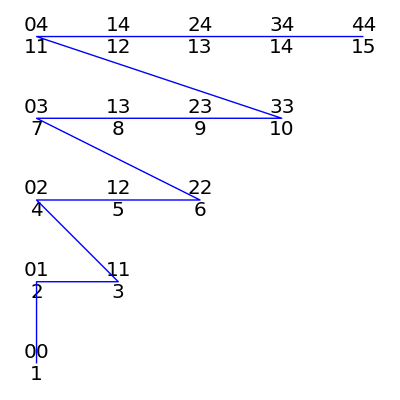

```mathematica
doubles=Table[{OrderedTupleFromIndex[index,2],index},{index,1,15}];
Graphics[{Text[Style[Column[{StringJoin[ToString/@#[[1]]],#[[2]]},
Alignment-> Center],20],#[[1]]]&/@doubles,Blue, Line[First/@doubles]}]
```

The ordered 2-tuple {4,4} has an index of  (4+0
1)+(4+1
2) +1=15 :

```mathematica
Binomial[4+0,1]+Binomial[4+1,2]+1
```

15

The structure of ordered 3-tuples in 3D:

```mathematica
triples=Table[{OrderedTupleFromIndex[index,3],index},{index,1,20}];
Graphics3D[{Text[Style[Column[{StringJoin[ToString/@#[[1]]],#[[2]]},
Alignment-> Center],20],#[[1]]]&/@triples,Blue, Line[First/@triples]}]
```

-Graphics3D-

### Properties and Relations

Use Tuples to produce ordered 3-tuples:

```mathematica
SortBy[Union[Sort/@Tuples[Range[0,2],{3}]],Reverse]
```

{{0,0,0},{0,0,1},{0,1,1},{1,1,1},{0,0,2},{0,1,2},{1,1,2},{0,2,2},{1,2,2},{2,2,2}}

The same sequence of ordered 3-tuples can be obtained from ordered Subsets:

```mathematica
#-{0,1,2}&/@SortBy[Subsets[Range[0,4],{3}],Reverse]
```

{{0,0,0},{0,0,1},{0,1,1},{1,1,1},{0,0,2},{0,1,2},{1,1,2},{0,2,2},{1,2,2},{2,2,2}}

OrderedTupleIndex returns the same ordered tuples in the same sequence:

```mathematica
Table[OrderedTupleFromIndex[index,3],{index,1,10}]
```

{{0,0,0},{0,0,1},{0,1,1},{1,1,1},{0,0,2},{0,1,2},{1,1,2},{0,2,2},{1,2,2},{2,2,2}}

## Source & Additional Information

### Contributed By

Ed Pegg Jr

### Keywords

index

tuples

subset

indexing

indexed subsets

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

Tuples

Subsets

SortBy

### Related Resource Objects

OrderedTupleIndex

SubsetIndex

SubsetFromIndex

TupleIndex

TupleFromIndex

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
OrderedTupleFromIndex[2019,5]
```

{0,0,1,3,10}

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.